## Equations

```mathematica
sys = {D[nH[t],t]==f*(W0+g*t)-tout*nH[t]+(1-(nH[t]/(Kh*(W0+g*t))))*rh*nH[t],nH[0]==0}
```

{nH'[t]==f (g t+W0)-tout nH[t]+rh nH[t] (1-nH[t]/(Kh (g t+W0))),nH[0]==0}

## Functions definition

### Exact (numerical) solutions

```mathematica
SolutionCalc[Rempl_]:=(Module[{tabT,TabRH,TabTout,TabF,TabK},
tabT=Rempl⟦;;,1,1,1,1,1⟧⟦;;,2⟧;
TabRH = Rempl⟦1,;;,1,1,1,2⟧⟦;;,2⟧;
TabTout = Rempl⟦1,1,;;,1,1,3⟧⟦;;,2⟧;
TabF= Rempl⟦1,1,1,;;,1,4⟧⟦;;,2⟧;
TabK= Rempl⟦1,1,1,1,;;,5⟧⟦;;,2⟧;
Table[nH[tabT[[itmax]]]/.NDSolve[sys/.Rempl⟦itmax,irh,itout,if,ik⟧,nH,{t,0,tabT[[itmax]]},MaxStepSize->0.0001][[1]],{itmax,1,Length[tabT]},{irh,1,Length[TabRH]},{itout,1,Length[TabTout]},{if,1,Length[TabF]},{ik,1,Length[TabK]}]])
```

```mathematica
SensitivityCalc[Rempl_,α_]:=(Module[{tabT,TabRH,TabTout,TabF,TabK,Solu,DTabRH,DTabTout,DTabF,DTabK,DRHRempl,DToutRempl,DFRempl,DKRempl,DRHSol,DToutSol,DFSol,DKSol,SensiRH,SensiTout,SensiF,SensiK,TabRHdim,TabToutdim,TabFdim,TabKdim,ElasRH,ElasTout,ElasF,ElasK},

tabT=Rempl⟦;;,1,1,1,1,1⟧⟦;;,2⟧;
TabRH = Rempl⟦1,;;,1,1,1,2⟧⟦;;,2⟧;
TabTout = Rempl⟦1,1,;;,1,1,3⟧⟦;;,2⟧;
TabF= Rempl⟦1,1,1,;;,1,4⟧⟦;;,2⟧;
TabK= Rempl⟦1,1,1,1,;;,5⟧⟦;;,2⟧;

TabRHdim=Table[TabRH[[irh]],{itmax,1,Length[tabT]},{irh,1,Length[TabRH]},{itout,1,Length[TabTout]},{if,1,Length[TabF]},{ik,1,Length[TabK]}];
TabToutdim=Table[TabTout[[itout]],{itmax,1,Length[tabT]},{irh,1,Length[TabRH]},{itout,1,Length[TabTout]},{if,1,Length[TabF]},{ik,1,Length[TabK]}];
TabFdim=Table[TabF[[if]],{itmax,1,Length[tabT]},{irh,1,Length[TabRH]},{itout,1,Length[TabTout]},{if,1,Length[TabF]},{ik,1,Length[TabK]}];
TabKdim=Table[TabK[[ik]],{itmax,1,Length[tabT]},{irh,1,Length[TabRH]},{itout,1,Length[TabTout]},{if,1,Length[TabF]},{ik,1,Length[TabK]}];

Solu = SolutionCalc[Rempl];

DTabRH = Rempl⟦1,;;,1,1,1,2⟧⟦;;,2⟧+α;
DTabTout = Rempl⟦1,1,;;,1,1,3⟧⟦;;,2⟧+α;
DTabF= Rempl⟦1,1,1,;;,1,4⟧⟦;;,2⟧+α;
DTabK = Rempl⟦1,1,1,1,;;,5⟧⟦;;,2⟧ + α;

DRHRempl =Table[{tmax->tabT⟦itmax⟧,rh-> DTabRH⟦irh⟧,tout->TabTout⟦itout⟧,f->TabF⟦if⟧,Kh->TabK[[ik]]},{itmax,1,Length[tabT]},{irh,1,Length[TabRH]},{itout,1,Length[TabTout]},{if,1,Length[TabF]},{ik,1,Length[TabK]}];
DToutRempl = Table[{tmax->tabT⟦itmax⟧,rh-> TabRH⟦irh⟧,tout->DTabTout⟦itout⟧,f->TabF⟦if⟧,Kh->TabK[[ik]]},{itmax,1,Length[tabT]},{irh,1,Length[TabRH]},{itout,1,Length[TabTout]},{if,1,Length[TabF]},{ik,1,Length[TabK]}];
DFRempl = Table[{tmax->tabT⟦itmax⟧,rh-> TabRH⟦irh⟧,tout->TabTout⟦itout⟧,f->DTabF⟦if⟧,Kh->TabK[[ik]]},{itmax,1,Length[tabT]},{irh,1,Length[TabRH]},{itout,1,Length[TabTout]},{if,1,Length[TabF]},{ik,1,Length[TabK]}];
DKRempl = Table[{tmax->tabT⟦itmax⟧,rh-> TabRH⟦irh⟧,tout->TabTout⟦itout⟧,f->TabF⟦if⟧,Kh->DTabK[[ik]]},{itmax,1,Length[tabT]},{irh,1,Length[TabRH]},{itout,1,Length[TabTout]},{if,1,Length[TabF]},{ik,1,Length[TabK]}];

DRHSol = SolutionCalc[DRHRempl];
DToutSol = SolutionCalc[DToutRempl];
DFSol = SolutionCalc[DFRempl];
DKSol = SolutionCalc[DKRempl];

SensiRH =(1/α)*(DRHSol-Solu);
SensiTout =(1/α)*(DToutSol-Solu);
SensiF =(1/α)*(DFSol-Solu);
SensiK =(1/α)*(DKSol-Solu);

ElasRH =(1/α)*(DRHSol-Solu)*TabRHdim/Solu;
ElasTout =(1/α)*(DToutSol-Solu)*TabToutdim/Solu;
ElasF =(1/α)*(DFSol-Solu)*TabFdim/Solu;
ElasK =(1/α)*(DKSol-Solu)*TabKdim/Solu;

{Solu,SensiRH,SensiTout,SensiF,SensiK,ElasRH,ElasTout,ElasF,ElasK}]
)
```

```mathematica
OptimalStrategy[Rempl_,α_]:=(Module[{tabT,TabRH,TabTout,TabF,TabK,Sensitivities,SensiRH,SensiTout,SensiF,SensiK,Opt,ElasRH,ElasTout,ElasF,ElasK,OptElas,Solu, Integrales},
tabT=Rempl⟦;;,1,1,1,1,1⟧⟦;;,2⟧;
TabRH = Rempl⟦1,;;,1,1,1,2⟧⟦;;,2⟧;
TabTout = Rempl⟦1,1,;;,1,1,3⟧⟦;;,2⟧;
TabF= Rempl⟦1,1,1,;;,1,4⟧⟦;;,2⟧;
TabK= Rempl⟦1,1,1,1,;;,5⟧⟦;;,2⟧;

Sensitivities = SensitivityCalc[Rempl,α];

Solu = Sensitivities[[1]];

SensiRH = Sensitivities[[2]];
SensiTout = Sensitivities[[3]];
SensiF = Sensitivities[[4]];
SensiK = Sensitivities[[5]];

ElasRH = Sensitivities[[6]];
ElasTout = Sensitivities[[7]];
ElasF = Sensitivities[[8]];
ElasK = Sensitivities[[9]];

Opt=Table[Sign[{SensiRH⟦itmax,irh,itout,if,ik⟧,SensiTout⟦itmax,irh,itout,if,ik⟧,SensiF⟦itmax,irh,itout,if,ik⟧,SensiK⟦itmax,irh,itout,if,ik⟧}⟦Position[Abs[{SensiRH⟦itmax,irh,itout,if,ik⟧,SensiTout⟦itmax,irh,itout,if,ik⟧,SensiF⟦itmax,irh,itout,if,ik⟧,SensiK⟦itmax,irh,itout,if,ik⟧}],Max[Abs[{SensiRH⟦itmax,irh,itout,if,ik⟧,SensiTout⟦itmax,irh,itout,if,ik⟧,SensiF⟦itmax,irh,itout,if,ik⟧,SensiK⟦itmax,irh,itout,if,ik⟧}]]]⟦1,1⟧⟧]*Position[Abs[{SensiRH⟦itmax,irh,itout,if,ik⟧,SensiTout⟦itmax,irh,itout,if,ik⟧,SensiF⟦itmax,irh,itout,if,ik⟧,SensiK⟦itmax,irh,itout,if,ik⟧}],Max[Abs[{SensiRH⟦itmax,irh,itout,if,ik⟧,SensiTout⟦itmax,irh,itout,if,ik⟧,SensiF⟦itmax,irh,itout,if,ik⟧,SensiK⟦itmax,irh,itout,if,ik⟧}]]]⟦1,1⟧,{itmax,1,Length[tabT]},{irh,1,Length[TabRH]},{itout,1,Length[TabTout]},{if,1,Length[TabF]},{ik,1,Length[TabK]}];

OptElas=Table[Sign[{ElasRH⟦itmax,irh,itout,if,ik⟧,ElasTout⟦itmax,irh,itout,if,ik⟧,ElasF⟦itmax,irh,itout,if,ik⟧,ElasK⟦itmax,irh,itout,if,ik⟧}⟦Position[Abs[{ElasRH⟦itmax,irh,itout,if,ik⟧,ElasTout⟦itmax,irh,itout,if,ik⟧,ElasF⟦itmax,irh,itout,if,ik⟧,ElasK⟦itmax,irh,itout,if,ik⟧}],Max[Abs[{ElasRH⟦itmax,irh,itout,if,ik⟧,ElasTout⟦itmax,irh,itout,if,ik⟧,ElasF⟦itmax,irh,itout,if,ik⟧,ElasK⟦itmax,irh,itout,if,ik⟧}]]]⟦1,1⟧⟧]*Position[Abs[{ElasRH⟦itmax,irh,itout,if,ik⟧,ElasTout⟦itmax,irh,itout,if,ik⟧,ElasF⟦itmax,irh,itout,if,ik⟧,ElasK⟦itmax,irh,itout,if,ik⟧}],Max[Abs[{ElasRH⟦itmax,irh,itout,if,ik⟧,ElasTout⟦itmax,irh,itout,if,ik⟧,ElasF⟦itmax,irh,itout,if,ik⟧,ElasK⟦itmax,irh,itout,if,ik⟧}]]]⟦1,1⟧,{itmax,1,Length[tabT]},{irh,1,Length[TabRH]},{itout,1,Length[TabTout]},{if,1,Length[TabF]},{ik,1,Length[TabK]}];

{Sensitivities,Opt,OptElas}])
```

```mathematica
listProduct[x_List]:=Times@@x
```

```mathematica
PlotHisto[TableOpt_]:=(
Module[{Opt,Talu,hm1,h1,h2,h3,h4,ParamPoints,L},
Opt=Flatten[TableOpt];
Talu=Tally[Opt];
ParamPoints=Length[Opt];
h1=If[Position[Talu[[;;,1]],1]≠{},Talu[[Position[Talu[[;;,1]],1][[1,1]],2]]/ParamPoints,0];
h2=If[Position[Talu[[;;,1]],-2]≠{},Talu[[Position[Talu[[;;,1]],-2][[1,1]],2]]/ParamPoints,0];
h3=If[Position[Talu[[;;,1]],3]≠{},Talu[[Position[Talu[[;;,1]],3][[1,1]],2]]/ParamPoints,0];
h4=If[Position[Talu[[;;,1]],4]≠{},Talu[[Position[Talu[[;;,1]],4][[1,1]],2]]/ParamPoints,0];
If[{-1,2,-3,-4}∩Talu[[;;,1]]≠{}||Max[Talu[[;;,1]]]>4||Min[Talu[[;;,1]]]<-4,Return["There is an unexpected strategy, look closer!"],
BarChart[{h1,h2,h3,h4},ChartLabels->{Rotate["increase rh",45 Degree],Rotate["decrease tout",45 Degree],Rotate["increase f",45 Degree],Rotate["increase K",45 Degree]},ChartStyle->{Black,Cyan,Magenta,Yellow},Frame->True,LabelStyle->{FontSize->16,Black}]]
])
```

```mathematica
Prop[TableOpt_]:=(
Module[{Opt,Talu,hm1,h1,h2,h3,h4,ParamPoints,L},
Opt=Flatten[TableOpt];
Talu=Tally[Opt];
ParamPoints=Length[Opt];
h1=If[Position[Talu[[;;,1]],1]≠{},Talu[[Position[Talu[[;;,1]],1][[1,1]],2]]/ParamPoints,0];
h2=If[Position[Talu[[;;,1]],2]≠{},Talu[[Position[Talu[[;;,1]],2][[1,1]],2]]/ParamPoints,0];
h3=If[Position[Talu[[;;,1]],3]≠{},Talu[[Position[Talu[[;;,1]],3][[1,1]],2]]/ParamPoints,0];
h4=If[Position[Talu[[;;,1]],4]≠{},Talu[[Position[Talu[[;;,1]],4][[1,1]],2]]/ParamPoints,0];
Return[{h1,h2,h3,h4}]
])
```

```mathematica
PropCol[TableOpt_]:=(
Module[{Opt,Talu,hm1,h1,h2,h3,h4,ParamPoints,L},
Opt=Flatten[TableOpt];
Talu=Tally[Opt];
ParamPoints=Length[Opt];
h1=If[Position[Talu[[;;,1]],1]≠{},Talu[[Position[Talu[[;;,1]],1][[1,1]],2]]/ParamPoints,0];
h2=If[Position[Talu[[;;,1]],2]≠{},Talu[[Position[Talu[[;;,1]],2][[1,1]],2]]/ParamPoints,0];
h3=If[Position[Talu[[;;,1]],3]≠{},Talu[[Position[Talu[[;;,1]],3][[1,1]],2]]/ParamPoints,0];
h4=If[Position[Talu[[;;,1]],4]≠{},Talu[[Position[Talu[[;;,1]],4][[1,1]],2]]/ParamPoints,0];
Return[{1-h2-h1,1-h3-h1,1-h4-h1}]
])
```

```mathematica
PropCol1[TableOpt_]:=(
Module[{Opt,Talu,hm1,h1,h2,h3,h4,ParamPoints,L},
Opt=Flatten[TableOpt];
Talu=Tally[Opt];
ParamPoints=Length[Opt];
h1=If[Position[Talu[[;;,1]],1]≠{},Talu[[Position[Talu[[;;,1]],1][[1,1]],2]]/ParamPoints,0];
h2=If[Position[Talu[[;;,1]],2]≠{},Talu[[Position[Talu[[;;,1]],2][[1,1]],2]]/ParamPoints,0];
h3=If[Position[Talu[[;;,1]],3]≠{},Talu[[Position[Talu[[;;,1]],3][[1,1]],2]]/ParamPoints,0];
h4=If[Position[Talu[[;;,1]],4]≠{},Talu[[Position[Talu[[;;,1]],4][[1,1]],2]]/ParamPoints,0];
Return[{1-h1,1-h1,1-h1}]
])
```

## Calculation on the refined parameter space

```mathematica
tmaxB={3.5};

(*Defined globally*)
g=711;(*=(2500-10)/3.5,rate per day*)
TabK=10^Table[i,{i,4,6.25,0.125}];
W0=10;

TabRH=10^Table[i,{i,-1,1.25,0.125}];
TabTout=10^Table[i,{i,-0.5,4,0.25}];
TabF=10^Table[i,{i,3,7.5,0.25}];
```

```mathematica
Rempl = Table[{tmax->tmaxB[[itmax]],rh->TabRH⟦irh⟧,tout-> TabTout⟦itout⟧,f->TabF⟦if⟧,Kh->TabK[[ik]]},{itmax,1,Length[tmaxB]},{irh,1,Length[TabRH]},{itout,1,Length[TabTout]},{if,1Length[TabF]},{ik,1,Length[TabK]}];
```

```mathematica
listProduct[Dimensions[Rempl]]
```

651605

```mathematica
{T0001,TestMore0001} = AbsoluteTiming[OptimalStrategy[Rempl,0.0001]];
```

```mathematica
Export["/Users/bansept/Documents/Recherche/Postdoc/Projects_Nancy/3.Morphotypes_paper/simulated_data"<>"/2022-06-04-TestMore0001.wdx",TestMore0001,"WDX"];
```

```mathematica
T0001
```

T0001

## Plots

```mathematica
TestMore0001 = Import["/Users/bansept/Documents/Recherche/Postdoc/Projects_Nancy/3.Morphotypes_paper/simulated_data"<>"/2022-06-04-TestMore0001.wdx","WDX"];
```

```mathematica
Dimensions[TestMore0001[[3]]]
```

{1,19,19,19,19}

```mathematica
TestMore0001[[3]]
```

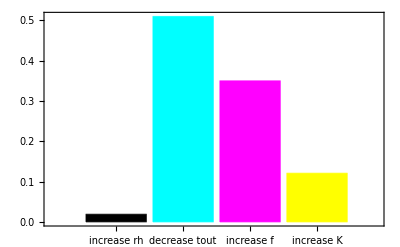

```mathematica
PlotHisto[TestMore0001[[3]]](*Elasticity*)
```

```mathematica
TabMinRHTout = Flatten[Table[{Log10[TabRH[[irh]]],Log10[TabTout[[itout]]],Log10[N[Min[Flatten[TestMore0001⟦1,1,1⟧⟦irh,itout,;;,;;⟧]]]]},{irh,1,Length[TabRH]},{itout,1,Length[TabTout]}],1];
TabMaxRHTout = Flatten[Table[{Log10[TabRH[[irh]]],Log10[TabTout[[itout]]],Log10[N[Max[Flatten[TestMore0001⟦1,1,1⟧⟦irh,itout,;;,;;⟧]]]]},{irh,1,Length[TabRH]},{itout,1,Length[TabTout]}],1];
```

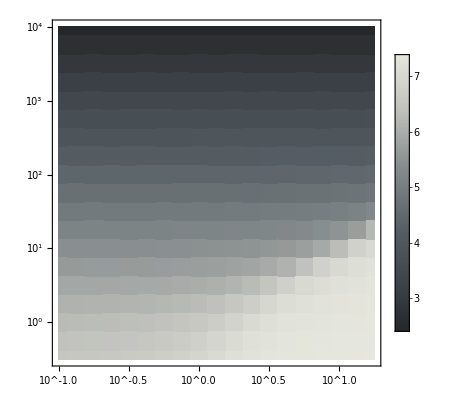

```mathematica
Show[{ListDensityPlot[TabMinRHTout,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["GrayTones"][Rescale[#,{2,7.5}]]&),PlotLegends->Automatic,PlotRange->All],ListContourPlot[TabMinRHTout,ContourShading->None,Contours->{9},ContourStyle->Directive[Cyan,Thick]]},BaseStyle->{FontSize->16},LabelStyle->{FontSize->20,Black},DataRange->{{-0.5,4},{-1.25,1}},AspectRatio->1,Frame->True,FrameTicks->{{{-1,"10^-1.0"},{-0.5,"10^-0.5"},{0,"10^0.0"},{0.5,"10^0.5"},{1,"10^1.0"}},{{-1,"10^-1"},{0,"10^0"},{1,"10^1"},{2,"10^2"},{3,"10^3"},{4,"10^4"}},None,None}]
```

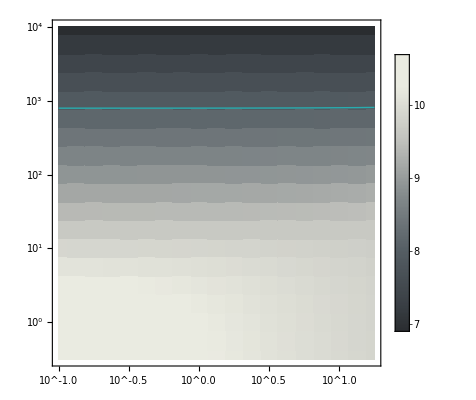

```mathematica
Show[{ListDensityPlot[TabMaxRHTout,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["GrayTones"][Rescale[#,{6.5,10.25}]]&),PlotLegends->Automatic,PlotRange->All],ListContourPlot[TabMaxRHTout,ContourShading->None,Contours->{8},ContourStyle->Directive[Cyan,Thick]]},BaseStyle->{FontSize->16},LabelStyle->{FontSize->20,Black},DataRange->{{-0.5,4},{-1.25,1}},AspectRatio->1,Frame->True,FrameTicks->{{{-1,"10^-1.0"},{-0.5,"10^-0.5"},{0,"10^0.0"},{0.5,"10^0.5"},{1,"10^1.0"}},{{-1,"10^-1"},{0,"10^0"},{1,"10^1"},{2,"10^2"},{3,"10^3"},{4,"10^4"}},None,None}]
```

```mathematica
ElasNorm=TestMore0001[[3,1]]/.{-2->2};
```

```mathematica
ArrayRHTout = Table[RGBColor[PropCol[ElasNorm[[irh,itout,;;,;;]]]],{irh,1,Length[TabRH]},{itout,1,Length[TabTout]}];
```

```mathematica
ArrayRHTout1 = Table[RGBColor[PropCol1[ElasNorm[[irh,itout,;;,;;]]]],{irh,1,Length[TabRH]},{itout,1,Length[TabTout]}];
```

```mathematica
ArrayRHF = Table[RGBColor[PropCol[ElasNorm[[irh,;;,if,;;]]]],{irh,1,Length[TabRH]},{if,1,Length[TabF]}];
```

```mathematica
ArrayRHF1 = Table[RGBColor[PropCol1[ElasNorm[[irh,;;,if,;;]]]],{irh,1,Length[TabRH]},{if,1,Length[TabF]}];
```

```mathematica
ArrayRHKh = Table[RGBColor[PropCol[ElasNorm[[irh,;;,;;,ik]]]],{irh,1,Length[TabRH]},{ik,1,Length[TabK]}];
```

```mathematica
ArrayRHKh1 = Table[RGBColor[PropCol1[ElasNorm[[irh,;;,;;,ik]]]],{irh,1,Length[TabRH]},{ik,1,Length[TabK]}];
```

```mathematica
ArrayToutF = Table[RGBColor[PropCol[ElasNorm[[;;,itout,if,;;]]]],{itout,1,Length[TabTout]},{if,1,Length[TabF]}];
ArrayToutF1 = Table[RGBColor[PropCol1[ElasNorm[[;;,itout,if,;;]]]],{itout,1,Length[TabTout]},{if,1,Length[TabF]}];ArrayToutKh = Table[RGBColor[PropCol[ElasNorm[[;;,itout,;;,ik]]]],{itout,1,Length[TabTout]},{ik,1,Length[TabK]}];
ArrayToutKh1 = Table[RGBColor[PropCol1[ElasNorm[[;;,itout,;;,ik]]]],{itout,1,Length[TabTout]},{ik,1,Length[TabK]}];ArrayFKh = Table[RGBColor[PropCol[ElasNorm[[;;,;;,if,ik]]]],{if,1,Length[TabF]},{ik,1,Length[TabK]}];
```

```mathematica
ArrayFKh1 = Table[RGBColor[PropCol1[ElasNorm[[;;,;;,if,ik]]]],{if,1,Length[TabF]},{ik,1,Length[TabK]}];
```

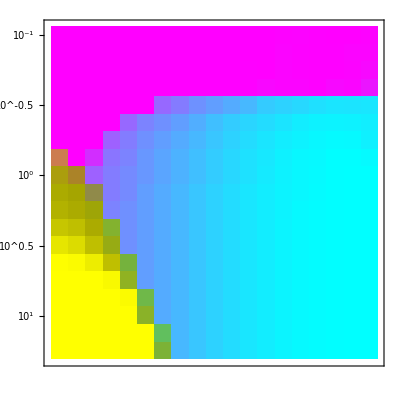

```mathematica
Rotate[Show[{ArrayPlot[ArrayRHTout,PlotLegends->Automatic,PlotRange->All,Frame->True,FrameTicks->{{{-1,Rotate["10^1",-90Degree]},{-0.5,Rotate["10^0.5",-90Degree]},{0,Rotate["10^0",-90Degree]},{0.5,Rotate["10^-0.5",-90Degree]},{1,Rotate["10^-1",-90Degree]}},None,None,{{-1,Rotate["10^-1",-90Degree]},{0,Rotate["10^0",-90Degree]},{1,Rotate["10^1",-90Degree]},{2,Rotate["10^2",-90Degree]},{3,Rotate["10^3",-90Degree]},{4,Rotate["10^4",-90Degree]}}},BaseStyle->{FontSize->16},LabelStyle->{FontSize->20,Black},DataRange->{{-0.5,4},{-1.25,1}},AspectRatio->1]}],90 Degree]
```

```mathematica
(*Just checking it is the right shape*)
```

```mathematica
TabOpt = Flatten[Table[{Log10[TabRH[[irh]]],Log10[TabTout[[itout]]],Mean[Flatten[ElasNorm⟦irh,itout,;;,;;⟧]]},{irh,1,Length[TabRH]},{itout,1,Length[TabTout]}],1];
```

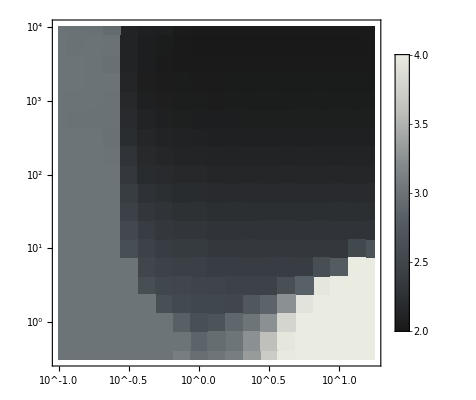

```mathematica
Show[{ListDensityPlot[TabOpt,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["GrayTones"][Rescale[#,{2,4}]]&),PlotLegends->Automatic,PlotRange->All],ListContourPlot[TabMinRHTout,ContourShading->None,Contours->{9},ContourStyle->Directive[Cyan,Thick]]},BaseStyle->{FontSize->16},LabelStyle->{FontSize->20,Black},DataRange->{{-0.5,4},{-1.25,1}},AspectRatio->1,Frame->True,FrameTicks->{{{-1,"10^-1.0"},{-0.5,"10^-0.5"},{0,"10^0.0"},{0.5,"10^0.5"},{1,"10^1.0"}},{{-1,"10^-1"},{0,"10^0"},{1,"10^1"},{2,"10^2"},{3,"10^3"},{4,"10^4"}},None,None}]
```

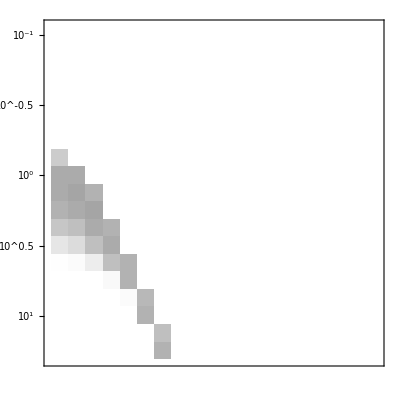

```mathematica
Rotate[Show[{ArrayPlot[ArrayRHTout1,PlotLegends->Automatic,PlotRange->All,Frame->True,FrameTicks->{{{-1,Rotate["10^1",-90Degree]},{-0.5,Rotate["10^0.5",-90Degree]},{0,Rotate["10^0",-90Degree]},{0.5,Rotate["10^-0.5",-90Degree]},{1,Rotate["10^-1",-90Degree]}},None,None,{{-1,Rotate["10^-1",-90Degree]},{0,Rotate["10^0",-90Degree]},{1,Rotate["10^1",-90Degree]},{2,Rotate["10^2",-90Degree]},{3,Rotate["10^3",-90Degree]},{4,Rotate["10^4",-90Degree]}}},BaseStyle->{FontSize->16},LabelStyle->{FontSize->20,Black},DataRange->{{-1,4},{-1.25,1}},AspectRatio->1]}],90 Degree]
```

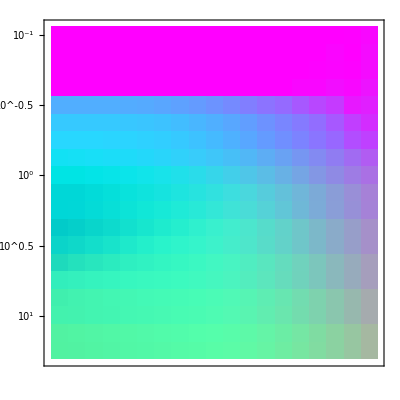

```mathematica
Rotate[Show[{ArrayPlot[ArrayRHF,PlotLegends->Automatic,PlotRange->All,Frame->True,FrameTicks->{{{-1,Rotate["10^1",-90Degree]},{-0.5,Rotate["10^0.5",-90Degree]},{0,Rotate["10^0",-90Degree]},{0.5,Rotate["10^-0.5",-90Degree]},{1,Rotate["10^-1",-90Degree]}},None,None,{{-1,Rotate["10^-1",-90Degree]},{0,Rotate["10^0",-90Degree]},{1,Rotate["10^1",-90Degree]},{2,Rotate["10^2",-90Degree]},{3,Rotate["10^3",-90Degree]},{4,Rotate["10^4",-90Degree]}}},BaseStyle->{FontSize->16},LabelStyle->{FontSize->20,Black},DataRange->{{-1,4},{-1.25,1}},AspectRatio->1]}],90 Degree]
```

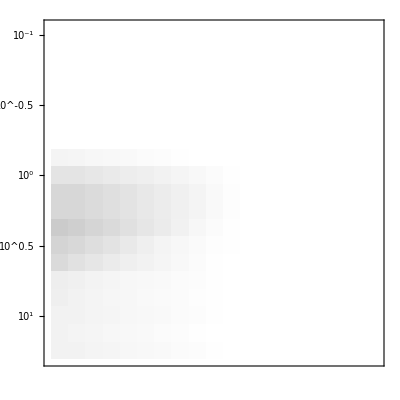

```mathematica
Rotate[Show[{ArrayPlot[ArrayRHF1,PlotLegends->Automatic,PlotRange->All,Frame->True,FrameTicks->{{{-1,Rotate["10^1",-90Degree]},{-0.5,Rotate["10^0.5",-90Degree]},{0,Rotate["10^0",-90Degree]},{0.5,Rotate["10^-0.5",-90Degree]},{1,Rotate["10^-1",-90Degree]}},None,None,{{-1,Rotate["10^-1",-90Degree]},{0,Rotate["10^0",-90Degree]},{1,Rotate["10^1",-90Degree]},{2,Rotate["10^2",-90Degree]},{3,Rotate["10^3",-90Degree]},{4,Rotate["10^4",-90Degree]}}},BaseStyle->{FontSize->16},LabelStyle->{FontSize->20,Black},DataRange->{{-1,4},{-1.25,1}},AspectRatio->1]}],90 Degree]
```

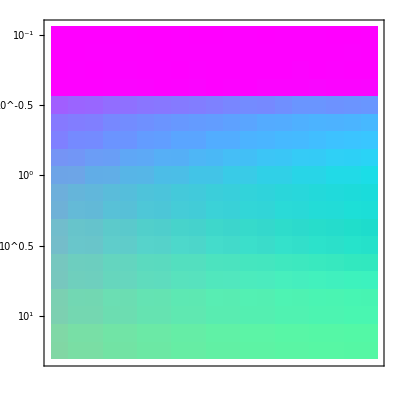

```mathematica
Rotate[Show[{ArrayPlot[ArrayRHKh,PlotLegends->Automatic,PlotRange->All,Frame->True,FrameTicks->{{{-1,Rotate["10^1",-90Degree]},{-0.5,Rotate["10^0.5",-90Degree]},{0,Rotate["10^0",-90Degree]},{0.5,Rotate["10^-0.5",-90Degree]},{1,Rotate["10^-1",-90Degree]}},None,None,{{-1,Rotate["10^-1",-90Degree]},{0,Rotate["10^0",-90Degree]},{1,Rotate["10^1",-90Degree]},{2,Rotate["10^2",-90Degree]},{3,Rotate["10^3",-90Degree]},{4,Rotate["10^4",-90Degree]}}},BaseStyle->{FontSize->16},LabelStyle->{FontSize->20,Black},DataRange->{{-1,4},{-1.25,1}},AspectRatio->1]}],90 Degree]
```

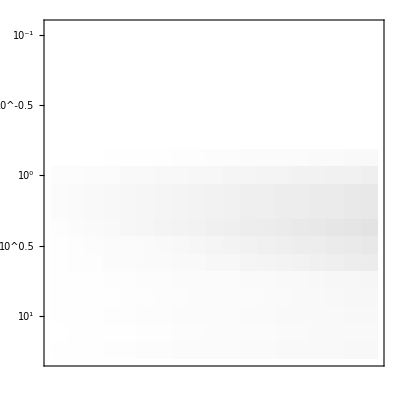

```mathematica
Rotate[Show[{ArrayPlot[ArrayRHKh1,PlotLegends->Automatic,PlotRange->All,Frame->True,FrameTicks->{{{-1,Rotate["10^1",-90Degree]},{-0.5,Rotate["10^0.5",-90Degree]},{0,Rotate["10^0",-90Degree]},{0.5,Rotate["10^-0.5",-90Degree]},{1,Rotate["10^-1",-90Degree]}},None,None,{{-1,Rotate["10^-1",-90Degree]},{0,Rotate["10^0",-90Degree]},{1,Rotate["10^1",-90Degree]},{2,Rotate["10^2",-90Degree]},{3,Rotate["10^3",-90Degree]},{4,Rotate["10^4",-90Degree]}}},BaseStyle->{FontSize->16},LabelStyle->{FontSize->20,Black},DataRange->{{-1,4},{-1.25,1}},AspectRatio->1]}],90 Degree]
```

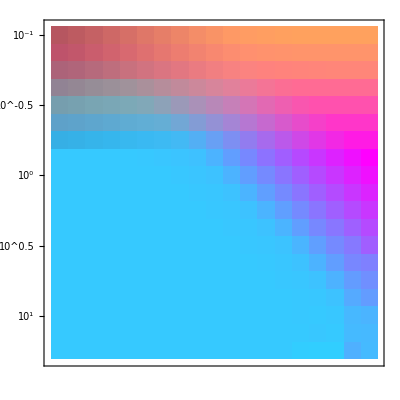

```mathematica
Rotate[Show[{ArrayPlot[ArrayToutF,PlotLegends->Automatic,PlotRange->All,Frame->True,FrameTicks->{{{-1,Rotate["10^1",-90Degree]},{-0.5,Rotate["10^0.5",-90Degree]},{0,Rotate["10^0",-90Degree]},{0.5,Rotate["10^-0.5",-90Degree]},{1,Rotate["10^-1",-90Degree]}},None,None,{{-1,Rotate["10^-1",-90Degree]},{0,Rotate["10^0",-90Degree]},{1,Rotate["10^1",-90Degree]},{2,Rotate["10^2",-90Degree]},{3,Rotate["10^3",-90Degree]},{4,Rotate["10^4",-90Degree]}}},BaseStyle->{FontSize->16},LabelStyle->{FontSize->20,Black},DataRange->{{-1,4},{-1.25,1}},AspectRatio->1]}],90 Degree]
```

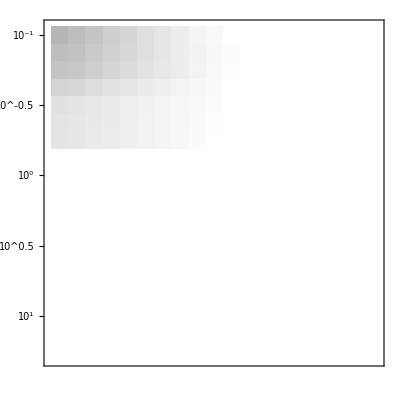

```mathematica
Rotate[Show[{ArrayPlot[ArrayToutF1,PlotLegends->Automatic,PlotRange->All,Frame->True,FrameTicks->{{{-1,Rotate["10^1",-90Degree]},{-0.5,Rotate["10^0.5",-90Degree]},{0,Rotate["10^0",-90Degree]},{0.5,Rotate["10^-0.5",-90Degree]},{1,Rotate["10^-1",-90Degree]}},None,None,{{-1,Rotate["10^-1",-90Degree]},{0,Rotate["10^0",-90Degree]},{1,Rotate["10^1",-90Degree]},{2,Rotate["10^2",-90Degree]},{3,Rotate["10^3",-90Degree]},{4,Rotate["10^4",-90Degree]}}},BaseStyle->{FontSize->16},LabelStyle->{FontSize->20,Black},DataRange->{{-1,4},{-1.25,1}},AspectRatio->1]}],90 Degree]
```

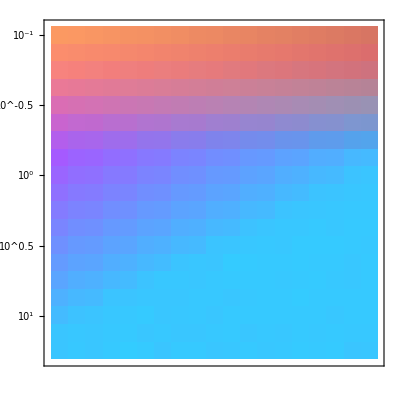

```mathematica
Rotate[Show[{ArrayPlot[ArrayToutKh,PlotLegends->Automatic,PlotRange->All,Frame->True,FrameTicks->{{{-1,Rotate["10^1",-90Degree]},{-0.5,Rotate["10^0.5",-90Degree]},{0,Rotate["10^0",-90Degree]},{0.5,Rotate["10^-0.5",-90Degree]},{1,Rotate["10^-1",-90Degree]}},None,None,{{-1,Rotate["10^-1",-90Degree]},{0,Rotate["10^0",-90Degree]},{1,Rotate["10^1",-90Degree]},{2,Rotate["10^2",-90Degree]},{3,Rotate["10^3",-90Degree]},{4,Rotate["10^4",-90Degree]}}},BaseStyle->{FontSize->16},LabelStyle->{FontSize->20,Black},DataRange->{{-1,4},{-1.25,1}},AspectRatio->1]}],90 Degree]
```

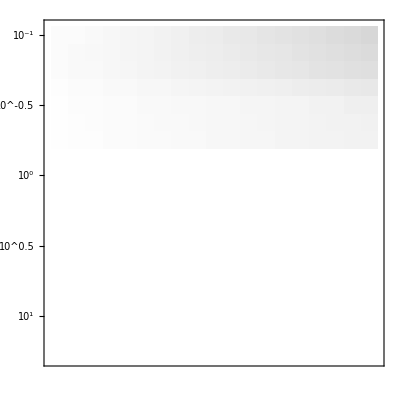

```mathematica
Rotate[Show[{ArrayPlot[ArrayToutKh1,PlotLegends->Automatic,PlotRange->All,Frame->True,FrameTicks->{{{-1,Rotate["10^1",-90Degree]},{-0.5,Rotate["10^0.5",-90Degree]},{0,Rotate["10^0",-90Degree]},{0.5,Rotate["10^-0.5",-90Degree]},{1,Rotate["10^-1",-90Degree]}},None,None,{{-1,Rotate["10^-1",-90Degree]},{0,Rotate["10^0",-90Degree]},{1,Rotate["10^1",-90Degree]},{2,Rotate["10^2",-90Degree]},{3,Rotate["10^3",-90Degree]},{4,Rotate["10^4",-90Degree]}}},BaseStyle->{FontSize->16},LabelStyle->{FontSize->20,Black},DataRange->{{-1,4},{-1.25,1}},AspectRatio->1]}],90 Degree]
```

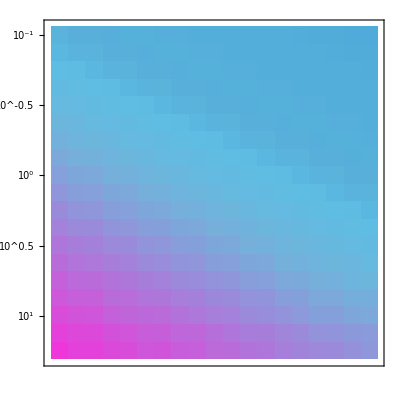

```mathematica
Rotate[Show[{ArrayPlot[ArrayFKh,PlotLegends->Automatic,PlotRange->All,Frame->True,FrameTicks->{{{-1,Rotate["10^1",-90Degree]},{-0.5,Rotate["10^0.5",-90Degree]},{0,Rotate["10^0",-90Degree]},{0.5,Rotate["10^-0.5",-90Degree]},{1,Rotate["10^-1",-90Degree]}},None,None,{{-1,Rotate["10^-1",-90Degree]},{0,Rotate["10^0",-90Degree]},{1,Rotate["10^1",-90Degree]},{2,Rotate["10^2",-90Degree]},{3,Rotate["10^3",-90Degree]},{4,Rotate["10^4",-90Degree]}}},BaseStyle->{FontSize->16},LabelStyle->{FontSize->20,Black},DataRange->{{-1,4},{-1.25,1}},AspectRatio->1]}],90 Degree]
```

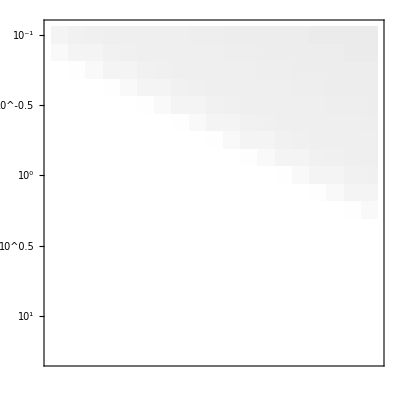

```mathematica
Rotate[Show[{ArrayPlot[ArrayFKh1,PlotLegends->Automatic,PlotRange->All,Frame->True,FrameTicks->{{{-1,Rotate["10^1",-90Degree]},{-0.5,Rotate["10^0.5",-90Degree]},{0,Rotate["10^0",-90Degree]},{0.5,Rotate["10^-0.5",-90Degree]},{1,Rotate["10^-1",-90Degree]}},None,None,{{-1,Rotate["10^-1",-90Degree]},{0,Rotate["10^0",-90Degree]},{1,Rotate["10^1",-90Degree]},{2,Rotate["10^2",-90Degree]},{3,Rotate["10^3",-90Degree]},{4,Rotate["10^4",-90Degree]}}},BaseStyle->{FontSize->16},LabelStyle->{FontSize->20,Black},DataRange->{{-1,4},{-1.25,1}},AspectRatio->1]}],90 Degree]
```

## Legend for RGB color scale

```mathematica
{error,xf}=FindGeometricTransform[{{0,0},{1,0},{1,Tan[Pi/3]}/2},{{0,0},{1,0},{0,1}}];
```

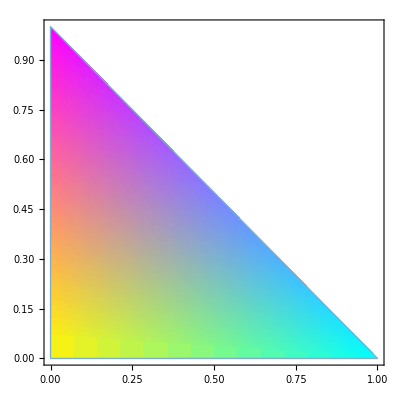

```mathematica
st=ParametricPlot[{u,v},{u,0,1},{v,0,1-u},ColorFunction->({x,y}↦RGBColor[1-x,1-y,x+y]),Mesh->None]
```

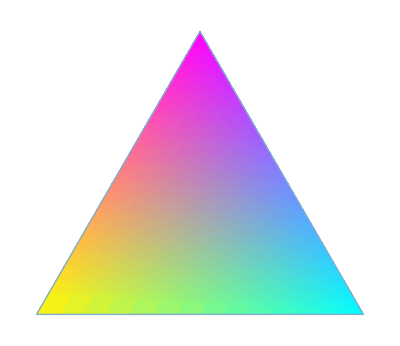

```mathematica
all=Graphics[GeometricTransformation[First@st,xf]]
```

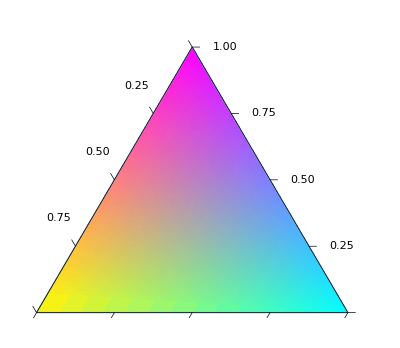

```mathematica
ClearAll[tickGraphics,triangleTicks];
Module[{ticklen=0.025,(*length of ticks (const parameter)*)textoffset=0.08},tickGraphics[tickrange:{0.,total_},angle_]:=With[{rotSideXF=RotationTransform[angle,total {1.,Tan[Pi/6]}/2.]},{Line[rotSideXF/@Thread[{tickrange,0}]],With[{rotTickXF=Composition[RotationTransform[π/3,rotSideXF@{#,0.}],rotSideXF]},{Text[NumberForm[N@#,{3,2}],rotTickXF[total {-ticklen-textoffset,0}+{#,0.}],{0,0.},BaseStyle->{FontSize->20}],{Line[rotTickXF/@{total {-ticklen,0}+{#,0.},{#,0.}}]}}]&/@Select[N@FindDivisions[tickrange,4],0.≤#≤total&]}];
triangleTicks[g_Graphics,total_:1]:=Show[Graphics[First@g],Graphics[{AbsoluteThickness[0.5],Table[tickGraphics[{0.,total},N@angle],{angle,0,4 Pi/3,2 Pi/3}]}],Axes->False,Frame->None,PlotRange->total {{0,1+2*ticklen},{0,Sqrt[3]/2+2*ticklen}},PlotRangePadding->0.07 total,PlotRangeClipping->False,ImagePadding->{{20,5},{20,5}}]]

triangleTicks[all]
```

```mathematica
ListPropTest=Table[RGBColor[{1-0.01*i,1-0.01*i,0-0.01*i}],{i,0,100}]
```

{RGBColor[{1., 1., 0.}],RGBColor[{0.99, 0.99, -0.01}],RGBColor[{0.98, 0.98, -0.02}],RGBColor[{0.97, 0.97, -0.03}],RGBColor[{0.96, 0.96, -0.04}],RGBColor[{0.95, 0.95, -0.05}],RGBColor[{0.94, 0.94, -0.06}],RGBColor[{0.9299999999999999, 0.9299999999999999, -0.07}],RGBColor[{0.92, 0.92, -0.08}],RGBColor[{0.91, 0.91, -0.09}],RGBColor[{0.9, 0.9, -0.1}],RGBColor[{0.89, 0.89, -0.11}],RGBColor[{0.88, 0.88, -0.12}],RGBColor[{0.87, 0.87, -0.13}],RGBColor[{0.86, 0.86, -0.14}],RGBColor[{0.85, 0.85, -0.15}],RGBColor[{0.84, 0.84, -0.16}],RGBColor[{0.83, 0.83, -0.17}],RGBColor[{0.8200000000000001, 0.8200000000000001, -0.18}],RGBColor[{0.81, 0.81, -0.19}],RGBColor[{0.8, 0.8, -0.2}],RGBColor[{0.79, 0.79, -0.21}],RGBColor[{0.78, 0.78, -0.22}],RGBColor[{0.77, 0.77, -0.23}],RGBColor[{0.76, 0.76, -0.24}],RGBColor[{0.75, 0.75, -0.25}],RGBColor[{0.74, 0.74, -0.26}],RGBColor[{0.73, 0.73, -0.27}],RGBColor[{0.72, 0.72, -0.28}],RGBColor[{0.71, 0.71, -0.29}],RGBColor[{0.7, 0.7, -0.3}],RGBColor[{0.69, 0.69, -0.31}],RGBColor[{0.6799999999999999, 0.6799999999999999, -0.32}],RGBColor[{0.6699999999999999, 0.6699999999999999, -0.33}],RGBColor[{0.6599999999999999, 0.6599999999999999, -0.34}],RGBColor[{0.6499999999999999, 0.6499999999999999, -0.35000000000000003}],RGBColor[{0.64, 0.64, -0.36}],RGBColor[{0.63, 0.63, -0.37}],RGBColor[{0.62, 0.62, -0.38}],RGBColor[{0.61, 0.61, -0.39}],RGBColor[{0.6, 0.6, -0.4}],RGBColor[{0.59, 0.59, -0.41000000000000003}],RGBColor[{0.5800000000000001, 0.5800000000000001, -0.42}],RGBColor[{0.5700000000000001, 0.5700000000000001, -0.43}],RGBColor[{0.56, 0.56, -0.44}],RGBColor[{0.55, 0.55, -0.45}],RGBColor[{0.54, 0.54, -0.46}],RGBColor[{0.53, 0.53, -0.47000000000000003}],RGBColor[{0.52, 0.52, -0.48}],RGBColor[{0.51, 0.51, -0.49}],RGBColor[{0.5, 0.5, -0.5}],RGBColor[{0.49, 0.49, -0.51}],RGBColor[{0.48, 0.48, -0.52}],RGBColor[{0.47, 0.47, -0.53}],RGBColor[{0.45999999999999996, 0.45999999999999996, -0.54}],RGBColor[{0.44999999999999996, 0.44999999999999996, -0.55}],RGBColor[{0.43999999999999995, 0.43999999999999995, -0.56}],RGBColor[{0.42999999999999994, 0.42999999999999994, -0.5700000000000001}],RGBColor[{0.42000000000000004, 0.42000000000000004, -0.58}],RGBColor[{0.41000000000000003, 0.41000000000000003, -0.59}],RGBColor[{0.4, 0.4, -0.6}],RGBColor[{0.39, 0.39, -0.61}],RGBColor[{0.38, 0.38, -0.62}],RGBColor[{0.37, 0.37, -0.63}],RGBColor[{0.36, 0.36, -0.64}],RGBColor[{0.35, 0.35, -0.65}],RGBColor[{0.33999999999999997, 0.33999999999999997, -0.66}],RGBColor[{0.32999999999999996, 0.32999999999999996, -0.67}],RGBColor[{0.31999999999999995, 0.31999999999999995, -0.68}],RGBColor[{0.30999999999999994, 0.30999999999999994, -0.6900000000000001}],RGBColor[{0.29999999999999993, 0.29999999999999993, -0.7000000000000001}],RGBColor[{0.29000000000000004, 0.29000000000000004, -0.71}],RGBColor[{0.28, 0.28, -0.72}],RGBColor[{0.27, 0.27, -0.73}],RGBColor[{0.26, 0.26, -0.74}],RGBColor[{0.25, 0.25, -0.75}],RGBColor[{0.24, 0.24, -0.76}],RGBColor[{0.22999999999999998, 0.22999999999999998, -0.77}],RGBColor[{0.21999999999999997, 0.21999999999999997, -0.78}],RGBColor[{0.20999999999999996, 0.20999999999999996, -0.79}],RGBColor[{0.19999999999999996, 0.19999999999999996, -0.8}],RGBColor[{0.18999999999999995, 0.18999999999999995, -0.81}],RGBColor[{0.17999999999999994, 0.17999999999999994, -0.8200000000000001}],RGBColor[{0.16999999999999993, 0.16999999999999993, -0.8300000000000001}],RGBColor[{0.16000000000000003, 0.16000000000000003, -0.84}],RGBColor[{0.15000000000000002, 0.15000000000000002, -0.85}],RGBColor[{0.14, 0.14, -0.86}],RGBColor[{0.13, 0.13, -0.87}],RGBColor[{0.12, 0.12, -0.88}],RGBColor[{0.10999999999999999, 0.10999999999999999, -0.89}],RGBColor[{0.09999999999999998, 0.09999999999999998, -0.9}],RGBColor[{0.08999999999999997, 0.08999999999999997, -0.91}],RGBColor[{0.07999999999999996, 0.07999999999999996, -0.92}],RGBColor[{0.06999999999999995, 0.06999999999999995, -0.93}],RGBColor[{0.05999999999999994, 0.05999999999999994, -0.9400000000000001}],RGBColor[{0.04999999999999993, 0.04999999999999993, -0.9500000000000001}],RGBColor[{0.040000000000000036, 0.040000000000000036, -0.96}],RGBColor[{0.030000000000000027, 0.030000000000000027, -0.97}],RGBColor[{0.020000000000000018, 0.020000000000000018, -0.98}],RGBColor[{0.010000000000000009, 0.010000000000000009, -0.99}],RGBColor[{0., 0., -1.}]}

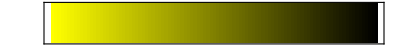

```mathematica
ArrayPlot[{ListPropTest,ListPropTest},PlotLegends->Automatic,PlotRange->All,Frame->True,FrameTicks->{None,None,None,{{0,Rotate["1.0",90Degree]},{0.5,Rotate[0.5,90Degree]},{1.0,Rotate["0.0",90 Degree]}}},BaseStyle->{FontSize->16},LabelStyle->{FontSize->20,Black},DataRange->{{0,1},{0,1}},AspectRatio->0.08]
```

```mathematica
ClearAll["Global`*"]
```